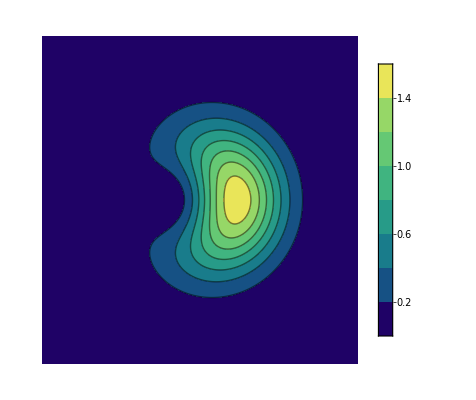
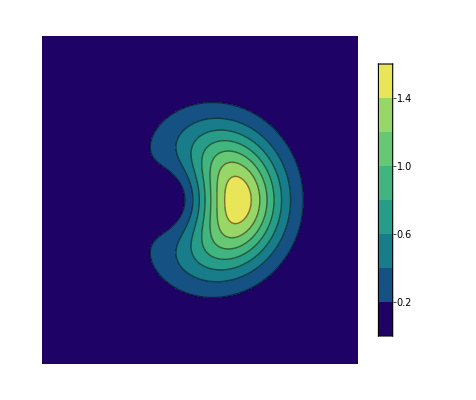
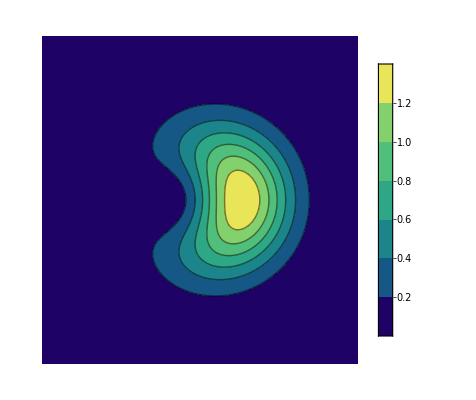
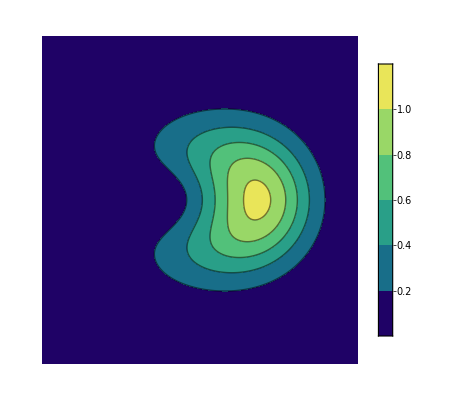
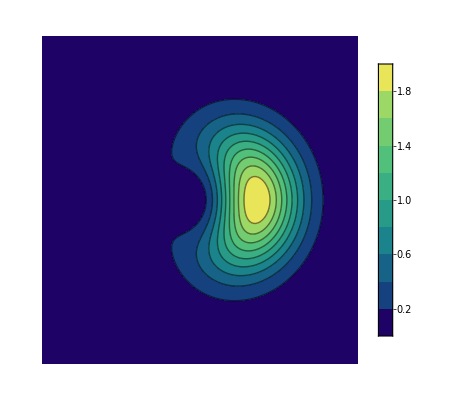
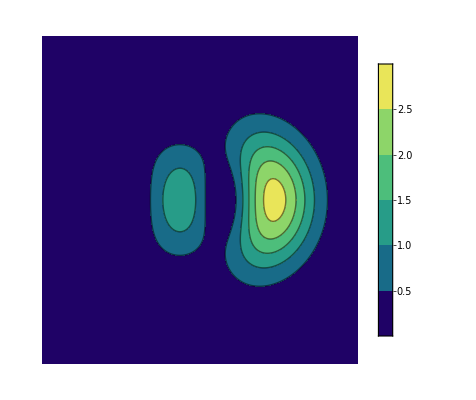
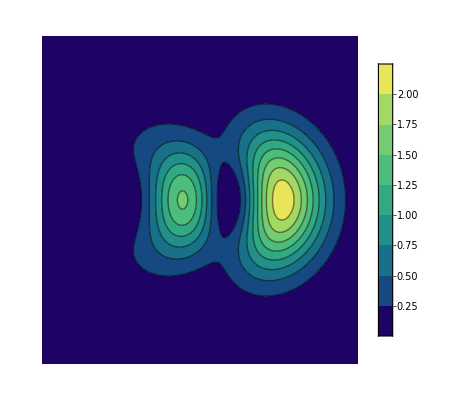
|  0 |  0.1 |  0.5 |  1
π/12 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
(11 π)/12 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ClearAll;
ClearAll["`*", Subscript, Derivative];
ClearAll["Global`*",Derivative,Subscript];
NN=(1/2(1+Abs[A]^2+(1-Abs[A]^2)Re[Subscript[P, 11]]))^(-1/2);
Subscript[P, 11]=1/(1+γ^2)(1-Γ γ √2 ⅈ Sin[φ]+γ^2(1-Γ^2/2))ⅇ^(-s^2/2);
s=Γ/2;
DP=NN 1/(√(1+γ^2))(((1-A)Subscript[M, 1]+(1+A)Subscript[M, 2])+(γ ⅇ^(ⅈ φ))/(√2)((1-A)Subscript[M, 3]+(1+A)Subscript[M, 4])+ⅈ (γ ⅇ^(ⅈ φ))/(√2)((1-A)Subscript[M, 5]+(1+A)Subscript[M, 6]));
 ϕ1=(1/(π*σ^2))^(1/4)ⅇ^(-s^2/2)ⅇ^(x^2/(2 σ^2))ⅇ^(-(x/σ-s/(√2))^2);
ϕ2=(1/(π*σ^2))^(1/4)ⅇ^(-s^2/2)ⅇ^(x^2/(2 σ^2))ⅇ^(-(x/σ+s/(√2))^2);
ψ=(1/(σ^2*π))^(1/4)ⅇ^(-y^2/(2 σ^2));
Subscript[M, 1]=ϕ2*ψ(*Subscript[ϕ, -s](x)Subscript[ϕ, 0](y)*);
Subscript[M, 2]=ϕ1*ψ(*Subscript[ϕ, s](x)Subscript[ϕ, 0](y)*);
Subscript[M, 3]=(s*ϕ2+1/σ(x*ϕ2-σ^2 D[ϕ2,x]))*ψ(*<x|-s,1>Subscript[ϕ, 0](y)*);
Subscript[M, 4]=(-s*ϕ1+1/σ(x*ϕ1-σ^2 D[ϕ1,x]))*ψ(*<x|s,1>Subscript[ϕ, 0](y)*);
Subscript[M, 5]=ϕ2*(1/σ(y*ψ-σ^2 D[ψ,y]))(*Subscript[ϕ, -s](x)Subscript[ϕ, 1](y)*);
Subscript[M, 6]=ϕ1*(1/σ(y*ψ-σ^2 D[ψ,y]))(*Subscript[ϕ, s](x)Subscript[ϕ, 1](y)*);
A=ⅇ^(ⅈ δ) Tan[α/2];
δ=0;
φ=0(*π/2*);
σ=1;
γ=1;
rlist={π/12,(11π)/12};
slist={0,0.1,0.5,1};

a=Table[ContourPlot[Abs[DP]^2,{x,-3,3},{y,-3,3},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotRange->All,Axes->False,Frame->False,PlotPoints->100,LabelStyle->{FontFamily->"Times",10,GrayLevel[0],Bold}],{α,rlist},{Γ,slist}];

grid=Table[Null,3,5];
grid[[2;;,2;;]]=a;
grid[[1,2;;]]=Table[TemplateApply[" <*Γ*>",<|"Γ"->Γ|>],{Γ,slist}];
grid[[2;;,1]]=Table[TemplateApply["<*α*>",InsertionFunction->ToString@*TraditionalForm],{α,rlist}];
v=Grid[grid,Frame->All,Alignment->Center]
```